```mathematica
(*obs = Flatten[Table[{Cos[θ]+0.4*RandomReal[]-0.2,Sin[θ]+0.4*RandomReal[]-0.2},{θ,0,2π,0.1},{j,10}],1];*)
obs = Table[{Cos[θ],Sin[θ]},{θ,0,2π,0.01}];
```

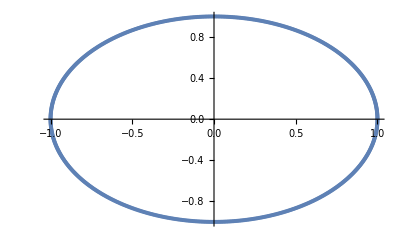

```mathematica
ListPlot[obs]
```

```mathematica
𝒟=SmoothKernelDistribution[obs,0.1]
```

DataDistribution[…]

```mathematica
Plot3D[PDF[𝒟,{x,y}],{x,-2,2},{y,-2,2},PlotRange->All]
```

-Graphics3D-

```mathematica
MutualInfo[𝒹_,{x_,x1_,x2_},{y_,y1_,y2_}]:=With[{
joint=PDF[𝒹,{x,y}],
m1=PDF[MarginalDistribution[𝒹,1],x],
m2=PDF[MarginalDistribution[𝒹,2],y]},
NIntegrate[joint*Log2[joint/(m1*m2)],{x,x1,x2},{y,y1,y2}, Method->"LocalAdaptive"]]
```

```mathematica
MutualInfo[𝒟,{x,-1,1},{y,-1,1}]
```

0.627804

```mathematica
Correlation[obs]
```

{{1.,-3.44731×10^-6},{-3.44731×10^-6,1.}}